```mathematica
Quit[]
```

# ABISS Test

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
SetProcess[{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]}];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/Tests/GTr_test/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/Tests/GTr_test/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/Tests/GTr_test/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/Tests/GTr_test/input/kinematics.m.

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish_var", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
process={F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]};
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
fieldsBorn=InsertFields[topologiesBorn, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish_var.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish_var} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

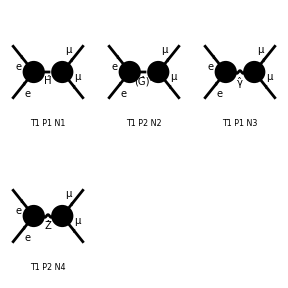

```mathematica
Paint[fieldsBorn];
```

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn,GaugeRules->{}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

```mathematica
myAmpBorn=ExtractAmplitude[ampBorn];
```

```mathematica
AmpSquare[myAmpBorn[[2]],myAmpBorn[[2]]]
```

(EL^4 gXll^4 me^2 mm^2 (-4 me^2+2 s+me^2 ABISS`Private`GTr[]) (-4 mm^2+2 s+mm^2 ABISS`Private`GTr[]))/(4 (s-mz^2 xi_bg)^2)